```mathematica
(*Vertices are labeled by {time index,Space index}*)
```

```mathematica
tsi[a_,SSSizes_]:=Position[Accumulate[SSSizes],_?(#>a-1&)][[1,1]]
ssi[a_,SSSizes_]:=a-Accumulate[Prepend[SSSizes,0]][[tsi[a,SSSizes]]]
globalIndex[ti_,si_,SSSizes_]:=Accumulate[Prepend[SSSizes,0]][[ti]]+si;

advanceOneSpatialslice [i_,SSSizes_]:=Mod[ssi[i,SSSizes],SSSizes[[tsi[i,SSSizes]]]]+1;
retreatOneSpatialslice [i_,SSSizes_]:=Mod[ssi[i,SSSizes]-2,SSSizes[[tsi[i,SSSizes]]]]+1;

SpaceAdjacentQ[i_,j_,SSSizes_]:=tsi[i,SSSizes]==tsi[j,SSSizes] && (ssi[i,SSSizes]==advanceOneSpatialslice[j,SSSizes])

TimeAdjacentQ[i_,j_,SSSizes_]:=Module[{TSMax},
TSMax = Length[SSSizes];(Mod[tsi[i,SSSizes],TSMax]+1==tsi[j,SSSizes])&& ((ssi[i,SSSizes]==advanceOneSpatialslice[j,SSSizes])||ssi[i,SSSizes]==ssi[j,SSSizes])]

(*hard non cyclic boundry conditions*)
(*
SpaceAdjacentQ[i_,j_,SSSizes_]:=tsi[i,SSSizes]==tsi[j,SSSizes] && (ssi[i,SSSizes]==ssi[j,SSSizes]+1)

TimeAdjacentQ[i_,j_,SSSizes_]:=Module[{TSMax},
TSMax = Length[SSSizes];(tsi[i,SSSizes]+1==tsi[j,SSSizes])&& ((ssi[i,SSSizes]==ssi[j,SSSizes]+1)||ssi[i,SSSizes]==ssi[j,SSSizes])]
*)
GenerateFlatSpaceTime[NumTimeSlices_,NumSpaceSlices_]:=Module[{NumVertices,AdjM,vertexList,SpaceSliceSizes},
SpaceSliceSizes = Table[NumSpaceSlices,{α,NumTimeSlices}];
NumVertices = NumSpaceSlices*NumTimeSlices;



AdjM = ConstantArray[0,{NumVertices,NumVertices}];
Do[If[TimeAdjacentQ[i,j,SpaceSliceSizes]||SpaceAdjacentQ[i,j,SpaceSliceSizes],AdjM[[i,j]]=1,Nothing];
,{i,1,NumVertices},{j,1,NumVertices}];
AdjM+=Transpose[AdjM];
<|AM-> AdjM,SSSizes->SpaceSliceSizes,TSMax-> NumTimeSlices,NVert-> NumVertices|>
]
```

```mathematica
Start = AbsoluteTime[];
ST = GenerateFlatSpaceTime[20,10];
GraphPlot3D[AdjacencyGraph[ST[AM]]]
AbsoluteTime[]-Start
```

-Graphics3D-

4.3117829

```mathematica
Move[ST_]:=Module[{randVert,randVertTSI,randVertSSI,emptyRow,emptyCol,SpaceSliceSizes,newVertGI,rightOfNewVert,leftOfRandVert,newAM,oldVertEdges,oldVertTimeLikeEdgePositions,oldVertFutureEdges,oldVertPastEdges,randFutureVert,randPastVert,NewSt},

randVert = RandomInteger[{1,ST[NVert]}];
randVertTSI = tsi[randVert,ST[SSSizes]];

emptyRow = ConstantArray[0,ST[NVert]];
emptyCol= ConstantArray[0,ST[NVert]+1];

SpaceSliceSizes = ReplacePart[ST[SSSizes],randVertTSI-> ST[SSSizes][[randVertTSI]]+1];

newAM = Insert[ Transpose[Insert[ST[AM],emptyRow,randVert+1]],emptyCol,randVert+1];






(*Step one get rid of the extra edge connecting the old vertex to the one on the other side of the newly split one*)

newVertGI = globalIndex[randVertTSI,advanceOneSpatialslice[randVert,SpaceSliceSizes],SpaceSliceSizes];

leftOfRandVert = globalIndex[randVertTSI,retreatOneSpatialslice[randVert,SpaceSliceSizes],SpaceSliceSizes];

rightOfNewVert = globalIndex[randVertTSI,advanceOneSpatialslice[newVertGI,SpaceSliceSizes],SpaceSliceSizes];




newAM[[randVert,rightOfNewVert]]=0;
newAM[[rightOfNewVert,randVert]]=0;


(* step two connect adjacent spatial edges*)

newAM[[randVert,newVertGI]]=1;
newAM[[newVertGI,randVert]]=1;

newAM[[ rightOfNewVert,newVertGI]]=1;
newAM[[newVertGI,rightOfNewVert]]=1;


(*step 3 select 1 random future timelike edge and 1 past timelike edge to split *)

oldVertEdges = newAM[[randVert]];

(*I Think there is a bug here that includes spacial edges!*)
oldVertEdgePositions = Flatten[Position[oldVertEdges,1]];

(*dont forget, this test doestn work for the cyclic edges!*)

oldVertFutureEdges = Select[oldVertEdgePositions,tsi[#,SpaceSliceSizes]>randVertTSI&];
oldVertPastEdges =Select[oldVertEdgePositions,tsi[#,SpaceSliceSizes]<randVertTSI&];


If[Length[oldVertFutureEdges]<1 ,
oldVertFutureEdges = Select[oldVertEdgePositions,tsi[#,SpaceSliceSizes]==1&];
oldVertPastEdges =Select[oldVertEdgePositions,tsi[#,SpaceSliceSizes]==ST[TSMax]-1&];
];

If[Length[oldVertPastEdges]<1,
oldVertPastEdges =Select[oldVertEdgePositions,tsi[#,SpaceSliceSizes]==ST[TSMax]&];
oldVertFutureEdges = Select[oldVertEdgePositions,tsi[#,SpaceSliceSizes]==2&];
];

(*debug info*)
(*
Print["randVert is "<>ToString[{tsi[randVert,SpaceSliceSizes],ssi[randVert,SpaceSliceSizes]}]];
Print["new Vert is "<>ToString[{tsi[newVertGI,SpaceSliceSizes],ssi[newVertGI,SpaceSliceSizes]}]];

Print["old Vert edges "<>ToString[Table[If[oldVertEdges[[i]]==1,{tsi[i,SpaceSliceSizes],ssi[i,SpaceSliceSizes]},Nothing],{i,ST[NVert]+1}]]];
Print["old Vert Future edges "<>ToString[Table[{tsi[i,SpaceSliceSizes],ssi[i,SpaceSliceSizes]},{i,oldVertFutureEdges}]]];
*)

randFutureVert = RandomChoice[oldVertFutureEdges];
randPastVert = RandomChoice[oldVertPastEdges];


newAM[[newVertGI,randFutureVert]] = 1;
newAM[[randFutureVert,newVertGI]] = 1;

newAM[[newVertGI,randPastVert]] = 1;
newAM[[randPastVert,newVertGI]] = 1;


(*Print[{randVertTSI,RandVertSSI}];*)
NewSt = <|AM-> newAM ,SSSizes->SpaceSliceSizes,TSMax-> ST[TSMax],NVert-> ST[NVert]+1|>

]

invMove[ST_]:=Module[{randVert,randVertTSI,trig,newAM,NewSt},

randVert = RandomInteger[{1,ST[NVert]}];
randVertTSI = tsi[randVert,ST[SSSizes]];

trig = 0;
newAM = Table[If[colIdx==randVert,trig=1;
                                                                            (*The code below this shouldnt be mode it should advance one spatial slice!*)
vec = ST[AM][[colIdx]]+ST[AM][[Mod[colIdx,ST[NVert]]+1]];Table[Boole[val≠ 0],{val,vec}],ST[AM][[colIdx+trig]]],{colIdx,ST[NVert]-1}];

trig = 0;
newAM = Table[If[rowIdx==randVert,trig=1;
                                                                            (*The code below this shouldnt be mode it should advance one spatial slice!*)vec =newAM[[;;,rowIdx]]+newAM[[;;,Mod[colIdx,ST[NVert]]+1]],newAM[[;;,rowIdx+trig]]];Table[Boole[val≠ 0],{val,vec}],{rowIdx,ST[NVert]-1}];

NewSt = <|AM-> newAM ,SSSizes->SpaceSliceSizes,TSMax-> ST[TSMax],NVert-> ST[NVert]+1|>
]
```

```mathematica
TIMax =10;
SIMax =5;
r1 = 12;
r2 =r1 SIMax/TIMax/1.5;
ST = GenerateFlatSpaceTime[TIMax,SIMax];
(*MatrixPlot[Move[ST]-origMoved]*)
(*mvd = Move[ST];*)
mvd = ST;
Do[mvd = invMove[mvd],{i,1}]

(*MatrixPlot[mvd[AM]]
MatrixPlot[ST[AM]]*)



SSSizeList = mvd[SSSizes];
a = AdjacencyGraph[mvd[AM],VertexCoordinates->Table[{tsi[i,mvd[SSSizes]](√3)/2,ssi[i,mvd[SSSizes]]+tsi[i,mvd[SSSizes]]1/2},{i,1,mvd[NVert]}],VertexLabels-> Table[i-> ToString[{tsi[i,SSSizeList],ssi[i,SSSizeList]}],{i,1,Length[mvd[AM]]}]];

Show[AdjacencyGraph[mvd[AM],VertexCoordinates->Table[{r1 Cos[(2 π tsi[i,mvd[SSSizes]])/mvd[TSMax]]+r2 Cos[(2 π (ssi[i,mvd[SSSizes]]+1/2 tsi[i,mvd[SSSizes]]))/(mvd[SSSizes]⟦tsi[i,mvd[SSSizes]]⟧)] Cos[(2 π tsi[i,mvd[SSSizes]])/mvd[TSMax]],r1 Sin[(2 π tsi[i,mvd[SSSizes]])/mvd[TSMax]]+r2 Cos[(2 π (ssi[i,mvd[SSSizes]]+1/2 tsi[i,mvd[SSSizes]]))/(mvd[SSSizes]⟦tsi[i,mvd[SSSizes]]⟧)] Sin[(2 π tsi[i,mvd[SSSizes]])/mvd[TSMax]],r2 Sin[(2 π (ssi[i,mvd[SSSizes]]+1/2 tsi[i,mvd[SSSizes]]))/(mvd[SSSizes]⟦tsi[i,mvd[SSSizes]]⟧)]},{i,1,mvd[NVert]}](*,VertexLabels-> Table[i-> ToString[{tsi[i,SSSizeList],ssi[i,SSSizeList]}],{i,1,Length[mvd[AM]]}]*)],ParametricPlot3D[{Sin[t] (r1+r2*.9*Min[1,(SIMax/7)]Cos[u]),Cos[t] (r1+r2*.9*Min[1,(SIMax/7)]Cos[u]),r2*.9*Min[1,(SIMax/7)]Sin[u]},{t,0,2 Pi},{u,0,2 Pi},PlotStyle-> Black,Mesh->None]]
```

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[SpaceSliceSizes].

Part::partw: Part 1 of {} does not exist.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[SpaceSliceSizes,0].

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[SpaceSliceSizes].

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[SpaceSliceSizes].

General::stop: Further output of Accumulate::normal will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[SpaceSliceSizes,0].

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[SpaceSliceSizes,0].

General::stop: Further output of Prepend::normal will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

AdjacencyGraph::matsq: Argument {{0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,1,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,1,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},«46»,{1,0,1,0,0,1,1,0,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0}} at position 1 is not a non-empty square matrix.

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[SpaceSliceSizes].

Part::partw: Part 1 of {} does not exist.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[SpaceSliceSizes,0].

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[SpaceSliceSizes].

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Accumulate::normal: Nonatomic expression expected at position 1 in Accumulate[SpaceSliceSizes].

General::stop: Further output of Accumulate::normal will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[SpaceSliceSizes,0].

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[SpaceSliceSizes,0].

General::stop: Further output of Prepend::normal will be suppressed during this calculation.

AdjacencyGraph::matsq: Argument {{0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,1,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,1,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},«46»,{1,0,1,0,0,1,1,0,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0}} at position 1 is not a non-empty square matrix.

Show::gcomb: Could not combine the graphics objects in ….

Show[AdjacencyGraph[{{0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,0,1,1,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},47,{1,0,1,0,0,1,1,0,0,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0}},VertexCoordinates→{1}],-Graphics3D-]
 |  |  |  |

```mathematica
Move[SmallFlatSpace_]:=Module[{},
Edges = EdgeList[SmallFlatSpace];
Vertices = VertexList[SmallFlatSpace];

(*Chose a random Vertex *)
RV=RandomChoice[Vertices];

(*generate a spacetime with that vertex removed*)
vremoved = VertexDelete[SmallFlatSpace,RV];

(*generate a graph of the selected vertex and its adjacent edges*)
selectedSubGraph = GraphDifference[SmallFlatSpace,vremoved];
selectedSubGraph = VertexDelete[selectedSubGraph,_?(VertexDegree[selectedSubGraph,#]<1&)];

(*modify the selected subgraph*)
EL = EdgeList[selectedSubGraph];
VL = VertexList[selectedSubGraph];

TimeSliceIndex = RV[[1]];
PastTimeSliceIndex = Mod[TimeSliceIndex-2,TSMax]+1;
FutureTimeSliceIndex = Mod[TimeSliceIndex,TSMax]+1;

AdjacentEdges = Select[EL,Function[x,x[[1,1]]==TimeSliceIndex && x[[2,1]]==TimeSliceIndex]];
PastEdges = Select[EL,Function[x,x[[1,1]]==PastTimeSliceIndex]];
FutureEdges = Select[EL,Function[x,x[[2,1]]==FutureTimeSliceIndex]];

AdjacentEdge = Select[AdjacentEdges,Function[x,x[[1]]==RV]][[1]];
RandomPastEdge = RandomChoice[PastEdges];
RandomFutureEdge = RandomChoice[FutureEdges];

NV ={TimeSliceIndex, RV[[2]]+(AdjacentEdge[[2,2]]- RV[[2]])/10};

OldEdges = DeleteCases[EL,x_/;x==AdjacentEdge||x>700];
NewEdges = {RV<->NV ,NV<->AdjacentEdge[[2]],RandomPastEdge[[1]]<->NV,NV<->RandomFutureEdge[[2]]};

ModifiedSelectedSubGraph = Graph[Join[OldEdges,NewEdges]];



(*add the modified removed vertex subgraph back to the spacetime*)
GraphUnion[vremoved,ModifiedSelectedSubGraph]
]
```

Part::partd: Part specification 35⟦1⟧ is longer than depth of object.

Part::partd: Part specification 25⟦1⟧ is longer than depth of object.

Part::partd: Part specification 26⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

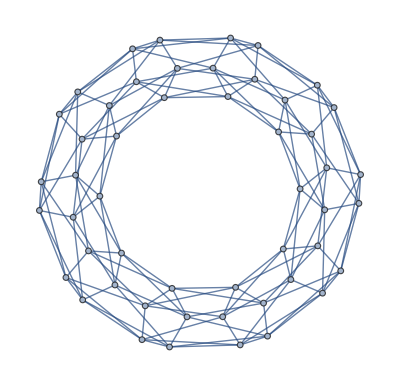

```mathematica
InverseMove[ST_]:=Module[{Edges,AdjacentVertices,RV,AdjacentVertex,Vertices,TimeSliceIndex},
Edges = EdgeList[ST];
Vertices = VertexList[ST];

(*Chose a random Vertex *)
RV=RandomChoice[Vertices];

TimeSliceIndex = RV[[1]];
AdjacentVertices = AdjacencyList[ST,RV];
AdjacentVertices = Select[AdjacentVertices,Function[x,x[[1]]==TimeSliceIndex ]];
AdjacentVertex = RandomChoice[AdjacentVertices];

SimpleGraph[Graph[DeleteCases[Vertices,RV],Edges/. RV-> AdjacentVertex]]

]
TSMax = 10;
SSMax =5;
SmallFlatSpace = GenerateFlatSpaceTime[SSMax,TSMax];
InverseMove[SmallFlatSpace]
```

```mathematica
NMoves[initialSpace_,n_]:=Nest[Move,initialSpace,n]
NInvMoves[initialSpace_,n_]:=Nest[InverseMove,initialSpace,n]
```

```mathematica
movedGraph = NInvMoves[NMoves[FlatSpace,25],25]
```

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Part::partw: Part 2 of RandomChoice[{}] does not exist.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

Part::partw: Part 2 of RandomChoice[{}] does not exist.

$Aborted

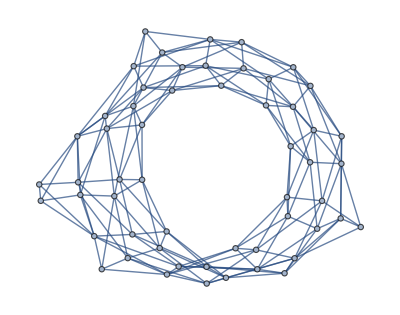

Module::lvsym: Local variable specification {Edges$,{{Vertices,TimeSliceIndex,AdjacentVertices}},RV$,AdjacentVertex$} contains {{Vertices,TimeSliceIndex,AdjacentVertices}}, which is not a symbol or an assignment to a symbol.

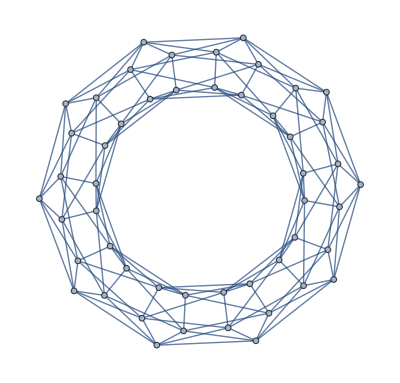
Module[{Edges$,{{Vertices,TimeSliceIndex,AdjacentVertices}},RV$,AdjacentVertex$},Edges$=EdgeList[-Graphics-];Vertices=VertexList[-Graphics-];RV$=RandomChoice[Vertices];TimeSliceIndex=RV$⟦1⟧;AdjacentVertices=AdjacencyList[RV$];AdjacentVertices=Select[AdjacentVertices,Function[x,x⟦1⟧==TimeSliceIndex]];AdjacentVertex$=RandomChoice[AdjacentVertices];SimpleGraph[Graph[DeleteCases[Vertices,RV$],Edges$/.RV$→AdjacentVertex$]]]

```mathematica
movedGraph = NMoves[SmallFlatSpace,5]
GG = EdgeDelete[SmallFlatSpace,Table[{i,1}<-> {i,2},{i,TSMax}]];
GraphPlot3D[movedGraph];
```

```mathematica
-Graphics-
"took 14 seconds to do 1000 inverse moves."
```

```mathematica
-Graphics-
"Takes ~9 minutes to generate"
```